## Panare 2DoF (RR):

```mathematica
Planare2dofITD[{qq1_,qq2_},x_,y_]:=Module[{hx,hy,JJ,hh,p,ll,F,q1,q2,T,L1,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
L1=1;
L2=1;
hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];

JJ={{D[hx,q1],D[hx,q2]},{D[hy,q1],D[hy,q2]}} ;

hh={{hx},{hy}} ;
p={{x},{y}} ;

F={{q1},{q2}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2} ;
Flatten[F]
]
```

```mathematica
Planare2dofIK[x_,y_]:=Module[{n,q1,q2,xx,yy},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1};
n=1000;
Do[Subscript[s, i]=Planare2dofITD[Subscript[s, i-1],x,y],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
xx=Cos[q1]+Cos[q1+q2];
yy=Sin[q1]+Sin[q1+q2];
{ListLinePlot[{xx,yy},PlotRange->All], ListLinePlot[{q1,q2},PlotRange->All]}
]
```

### test:

```mathematica
Planare2dofITD[{1,1},1/2,1/2]
```

{0.984625,1.02547}

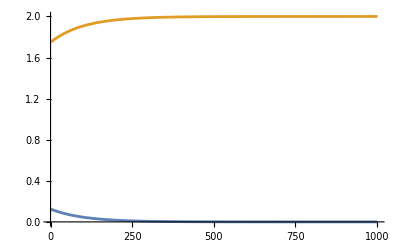
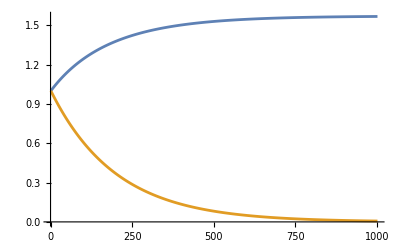

```mathematica
Planare2dofIK[0,2]
```

## Cartesiano 3DoF (PPP):

```mathematica
Cartesiano3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
hx=q1;
hy=q2;
hz=q3;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Cartesiano3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={0,0,0};
n=1000;
Do[Subscript[s, i]=Cartesiano3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=q1;
yy=q2;
zz=q3;
{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Cartesiano3dofITD[{1,1,1},1,1,1]
```

{1.,1.,1.}

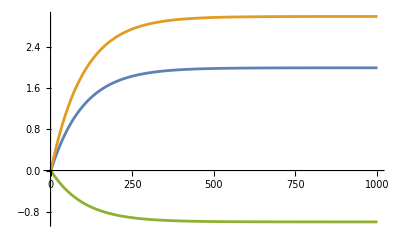
{-Graphics-,-Graphics-}

```mathematica
Cartesiano3dofIK[2,3,-1]
```

## Cilindrico 3DoF (RPP):

```mathematica
Cilindrico3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;

hx=-q3*Sin[q1];
hy=q3*Cos[q1];
hz=D1+q2;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Cilindrico3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={2,3,2};
n=1000;
Do[Subscript[s, i]=Cartesiano3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=-q3*Sin[q1];
yy=q3*Cos[q1];
zz=1+q2;
ListLinePlot[{xx,yy,zz},PlotRange->All]
]
```

### test:

```mathematica
Cilindrico3dofITD[{1,2,3},4,5,6]
```

{0.978771,2.03,2.96336}

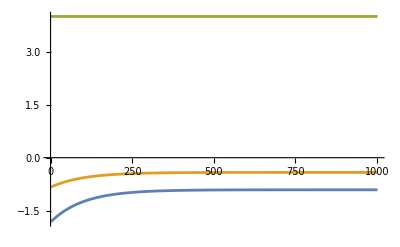

```mathematica
Cilindrico3dofIK[2,3,1]
```